```mathematica
ClearAll["Global`*"];
(*Au=f*)
f[x_]:=x;
A[u_]:={
func[x_]:=u/.y->x;
b=D[func[x],{x,2}]+func[x];
b
}
(*аналитическое решение дифференциального уравнения*)
sol=DSolve[{A[u[x]]⟦1⟧==f[x],u[0]==0,u[1]==0},u[x],x];
u[x_]=u[x]/.sol[[1]];

n=5;(*кол-во базисных функций*)
Array[ϕ,n];
Array[ψ,n];
(*For[i=1,i≤n,i++,
ϕ[i]=Sin[π i x ];
]*)
For[i=1,i≤n,i++,
ϕ[i]=x(1-x) x^(i-1);
]
```

```mathematica
(*Метод Бубнова*)
```

```mathematica
ψ=ϕ;
R=Table[NIntegrate[ψ[j]*A[ϕ[i]]⟦1⟧,{x,0,1}],{i,n},{j,n}];
μ=Table[NIntegrate[ψ[j]*f[x],{x,0,1}],{j,n}];
c=LinearSolve[R,μ];
u1[x_]:=∑_(i=1)^n c⟦i⟧ϕ[i];
```

```mathematica
(*Метод Галеркина*)
For[i=1,i≤n,i++,
ψ[i]=Sin[π i x ];
]
R=Table[NIntegrate[ψ[i]*A[ϕ[j]]⟦1⟧,{x,0,1}],{i,n},{j,n}];
μ=Table[NIntegrate[ψ[j]*f[x],{x,0,1}],{j,n}];
c=LinearSolve[R,μ];
u1[x_]:=∑_(i=1)^n c⟦i⟧ϕ[i];
```

```mathematica
(*МНК*)
For[i=1,i≤n,i++,
ψ[i]=A[ϕ[i]]⟦1⟧;
]
R=Table[NIntegrate[ψ[j]*A[ϕ[i]]⟦1⟧,{x,0,1}],{i,n},{j,n}];
μ=Table[NIntegrate[ψ[j]*f[x],{x,0,1}],{j,n}];
c=LinearSolve[R,μ];
u1[x_]:=∑_(i=1)^n c⟦i⟧ϕ[i];
```

```mathematica
(*Метод коллокаций в точках*)
Array[c,n];a={};
u1[x_]=∑_(i=1)^n c[i]ϕ[i];
h=1/(n+1);
R={};
For[k=1,k≤n,k++,{AppendTo[R,(A[u1[x]]⟦1⟧-f[x]==0)/.x->k h],AppendTo[a,c[k]]}];
sol=NSolve[R,a];
a=a/.sol[[1]];
u1[x_]=∑_(i=1)^n a⟦i⟧ϕ[i];
```

```mathematica
(*Метод коллокаций в подобластях*)
Array[c,n];a={};
u1[x_]=∑_(i=1)^n c[i]ϕ[i];
h=1/(n+1);
R={};
For[k=1,k≤n,k++,{AppendTo[R,Integrate[A[u1[x]][[1]]-f[x],{x,(k-1)h,k h}]==0],AppendTo[a,c[k]]}];
sol=NSolve[R,a];
a=a/.sol[[1]];
u1[x_]=∑_(i=1)^n a[[i]]ϕ[i];
```

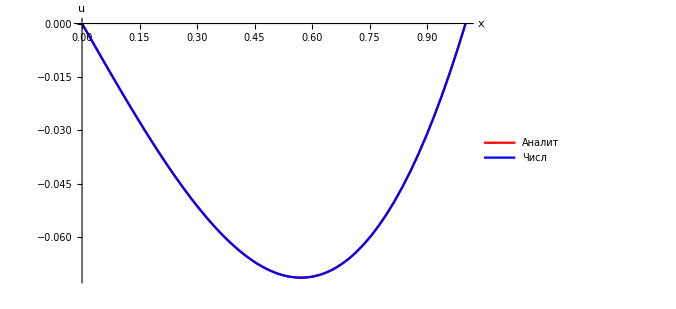

Абсолютная ошибка=

6.72286×10^-7

Относительная ошибка=

0.00001315

Невязка=

0.0000651858

```mathematica
(*График решения*)
Plot[{u[x],u1[x]},{x,0,1},AxesStyle->Thick,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotLegends->{"Аналит","Числ"},LabelStyle->Directive[20],AxesLabel->{"x","u"},ImageSize->500,PlotRange->All]
(*Абсолютная ошибка*)
Print["Абсолютная ошибка="]; √NIntegrate[(u[x]-u1[x])^2,{x,0,1}]
(*Относительная ошибка*)
Print["Относительная ошибка="]; (√NIntegrate[(u[x]-u1[x])^2,{x,0,1}])/(√NIntegrate[(u[x])^2,{x,0,1}])
(*Невязка*)
Print["Невязка="];√NIntegrate[(A[u1[x]][[1]]-f[x])^2,{x,0,1}]
```